```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
<<IGraphM`;
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
(*https://mathematica.stackexchange.com/questions/18625/avoiding-grid-lines-inside-filled-area-in-regionplot-exported-as-pdf*)
```

## Building (stationary) adjacency graph

```mathematica
db = DatabaseReference[FindFile[NotebookDirectory[]<>"/../data/genova.db"]]

(* We select the absolute, treat F and T roads as the same. This simplifies graph and reduces computation time. Since data is bad anyways, I don't think this will affect the results by much.*)
queryGraphLinks = ExternalEvaluate[db, "
	WITH e(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	), g(edge_id, node_from_id, node_to_id) AS (
		SELECT geo_edges.edge_id, geo_edges.node_from_id, geo_edges.node_to_id
		FROM geo_edges
		
	)
	SELECT ABS(g.edge_id) as \"from\", ABS(e.edge_id) AS \"to\"
	FROM e
	INNER JOIN g
	WHERE e.node_to_id = g.node_from_id AND ABS(g.edge_id) <> ABS(e.edge_id)
	UNION
	SELECT ABS(e.edge_id) AS \"from\", ABS(g.edge_id) as \"to\"
	FROM e
	INNER JOIN geo_edges g
	WHERE e.node_from_id = g.node_to_id AND ABS(g.edge_id) <> ABS(e.edge_id)
;"];

(* We select max because we are interested on the study of the congested direction of the road*)
queryTrafficData = ExternalEvaluate[db, "
	SELECT
		g.edge_id AS edge_id,
		MAX(t.count_mean) AS count
	FROM geo_edges g
	INNER JOIN traffic_data t
	ON g.edge_id = ABS(t.edge_id)
	WHERE t.hour_slot = 170
	GROUP BY g.edge_id
;"];

graphLinks = Thread[#["from"]<-> #["to"] /. #]&/@Normal[queryGraphLinks];
g=Graph[graphLinks[[;;]],VertexLabels->None];
validNodes = queryTrafficData[[;;, 1]];
invalidNodes = Select[VertexList[g], !MemberQ[validNodes, #]&];
g = VertexDelete[g, invalidNodes];
disconnectedNodes = Flatten[ConnectedComponents[g][[2;;]]]; (* Remove disconnected train network *)
g = VertexDelete[g, disconnectedNodes];
```

DatabaseReference[…]

## Graph plots

```mathematica
Rasterize[GraphPlot[g], RasterSize->1000]
```

-Graphics-

```mathematica
Count[VertexDegree[g], 2] (* Are there relatively few nodes with only two degrees? Can we go on without simplifying the graph? *)
```

530

## Getting parameters from data

### Get car counts

```mathematica
GetTrafficAtHour = (hour)↦ExternalEvaluate[db, "
	with tmp(edge_id, count) AS (
		SELECT g.edge_id AS edge_id,
		MAX(t.count_mean) AS count
		FROM geo_edges g
		INNER JOIN traffic_data t
		ON g.edge_id = ABS(t.edge_id)
		WHERE t.hour_slot = "<>ToString[hour]<>"
		GROUP BY g.edge_id
	)
	SELECT tmp.edge_id, tmp.count/(SELECT SUM(tmp.count) FROM tmp) AS fraction
	FROM tmp
	ORDER BY edge_id
;"]; (* TODO check ordering *)
```

### Get road geo position

```mathematica
BinarySearch = ResourceFunction["BinarySearch"];

GetRoadCoordinates = (g)↦Module[{edgeList, query,  queryIds, coordsPosition, data},
edgeList = VertexList@g;

query = ExternalEvaluate[db, "
		SELECT edge_id, AVG(lat) AS lat, AVG(lon) AS long
		FROM geo_nodes n
		INNER JOIN geo_edges e ON node_to_id = n.id OR node_from_id = n.id
		GROUP BY edge_id
		ORDER BY edge_id
	;"];

queryIds = Normal@query[[;;, 1]];
coordsPosition = ParallelMap[BinarySearch[queryIds, #] &, edgeList];

data = {Normal@query[[;;, 2]], Normal@query[[;;,3]]} // Transpose ;
ParallelMap[GeoPosition@data[[#]]&, coordsPosition]
];
```

### Naive rates method

```mathematica
ToAssociations = ResourceFunction["ToAssociations"];

ClearAll["NaiveRateMatrix"];
NaiveRateMatrix[hour_, g_]:=Module[{trafficData, neighborsOf, carProbs, wMatNaive},
trafficData = GetTrafficAtHour[hour];

neighborsOf = ToAssociations[# ->VertexList@NeighborhoodGraph[g, #] &/@ VertexList[g]]; (* Each vertex is also a neighbor of itself*)
carProbs =ToAssociations[ #["edge_id"]->#["fraction"]&/@ Normal[trafficData]];

wMatNaive = Table[Table[0, {i, 1, VertexCount@g}], {i, 1, VertexCount@g}];
SetSharedVariable[wMatNaive];

ParallelDo[Module[{neighbors, vertexId, counts, total, probs,  ids, i},
neighbors = neighborsOf[vertex];
vertexId = Position[VertexList@g, vertex][[1, 1]];

counts = carProbs[#] &/@ neighbors; (* Add a small fraction to prevent /0 errors *)
total = Total[counts];
If[total == 0, probs = Table[1/Length@neighbors, Length@neighbors], probs = counts / total];

ids = Flatten[Position[VertexList@g, # ] &/@ neighbors, 3];
For[i = 1, i <= Length@ids, i++, 
wMatNaive[[ids[[i]], vertexId]] = probs[[i]]
]
], {vertex, VertexList@g}];

wMatNaive
];
```

### Thresholds heuristics

```mathematica
BinarySearch = ResourceFunction["BinarySearch"];

GetRoadThresholds = (g)↦Module[{query, edgeList, data, queryIds, thresholdPositions}, 
(* 3.5m is the average car length in italy *)
edgeList = VertexList@g; (*Vertices in the graph are edges in the db*)

query = ExternalEvaluate[db, "
		SELECT edge_id, edge_length / 3.5 * speed / 50 as threshold
		FROM geo_edges
		ORDER BY edge_id
	;"];
queryIds = Normal@query[[;;, 1]];
thresholdPositions = ParallelMap[BinarySearch[queryIds, #] &, edgeList];

query[[#, 2]] &/@ thresholdPositions
];
```

## Simulating the thing

### Agent based random walk algorithm

For a left stochastic matrix, each column sums to 1.  Values are the probability of moving from node=column to node=row.

Algorithm:
1) Move each agent
2) Check if any node fails
3) immediately, redistribute agents, propagate avalanche
4) End simulation

```mathematica
On[Assert]

ClearAll["Pop"];
SetAttributes[Pop,HoldFirst];
Pop[list_]:=With[{item=list[[1]]},list=Delete[list,1];item];

ClearAll["Simulate"];
Simulate[rateMatrix_, nodeThresholds_, startingAgentPositions_, maxSteps_] := Module[{MoveAgents, AreThereFailures , ComputeAvalancheSize, i, nNodes, nAgents, carCountsByNode, agentPositions, possibleAgentPositions, failedNodes},
nNodes = Length[rateMatrix];
If[nNodes != Length[nodeThresholds], Return[$Failed]];

possibleAgentPositions = Table[i, {i, 1, nNodes}];
nAgents = Length[agentPositions];
agentPositions = startingAgentPositions;	

MoveAgents[] := Module[{},
agentPositions = (
Assert[Total[rateMatrix[[;;, #]]] == 1];
RandomChoice[rateMatrix[[;;, #]]->possibleAgentPositions ]
) &/@ agentPositions;
];

AreThereFailures[] := Module[{},
carCountsByNode = Count[agentPositions, #] &/@ Table[i, {i, 1, nNodes}];
failedNodes = Append[(Transpose@Position[# < 0 &/@ (nodeThresholds -carCountsByNode ), True]), {}][[1]];

If[Length[failedNodes]>0, Return[True]];
False
];

ComputeAvalancheSize[node_] := Module[{avalancheSize, carCount, avalancheCarCounts, adjacentNodes, nodesToCheck, lockedNodes, currentNode, newNode, transitionProbabilities},
nodesToCheck = {node};
lockedNodes = {};
avalancheCarCounts = carCountsByNode;


While[Length@nodesToCheck >0,
currentNode = Pop[nodesToCheck];
Assert[avalancheCarCounts[[currentNode]] >0, "carCount"];

If[nodeThresholds[[currentNode]] -avalancheCarCounts[[currentNode]] >=0, Continue[]];

AppendTo[lockedNodes, currentNode];

If[Length@lockedNodes == nNodes, Break[]];

transitionProbabilities = Normal@rateMatrix[[currentNode]];
(transitionProbabilities[[#]] = 0 )&/@ lockedNodes;

(* If there is nowhere to go, we just lock this node and no transfer*)
If[Total@transitionProbabilities == 0,
Continue[];
];

transitionProbabilities /= Total[transitionProbabilities];

For[carCount = avalancheCarCounts[[currentNode]], carCount >0, carCount--,
Assert[nNodes == Length@transitionProbabilities, "nNodes"];

newNode = RandomChoice[transitionProbabilities->Table[x, {x, 1, nNodes}]];

Assert[newNode != currentNode, "currentNode"];
Assert[!MemberQ[lockedNodes, newNode], "lockedNodes"];
If[!MemberQ[nodesToCheck, newNode], AppendTo[nodesToCheck, newNode]];

avalancheCarCounts[[newNode]]++;
avalancheCarCounts[[currentNode]]--;
];
];

Assert[Total[avalancheCarCounts] == Total[carCountsByNode]];

Return[{node,Length@lockedNodes}];
];

For[i=1, i<=maxSteps,  i++, 
MoveAgents[];

If[!AreThereFailures[], Continue[]];
Break[];
];

If[Length@failedNodes == 0, Return[{}]];

Map[ComputeAvalancheSize, failedNodes]
];
```

### Demo data generation functions

```mathematica
ClearAll["GenerateAgents"];
GenerateAgents [nAgents_, nNodes_] := Table[RandomInteger[{1, nNodes}], nAgents];

ClearAll["SampleMarkovMatrix"];
SampleMarkovMatrix[n_,min_:0]:=If[min n<1,Transpose@RandomPoint[Simplex[IdentityMatrix[n](1-min n)],n]+min,$Failed];

ClearAll["SampleThresholds"];
SampleThresholds = (n) ↦ Table[RandomInteger[{2, Floor@Sqrt@n}], n];
```

### Running the simulation for demo graph

Starting simulation

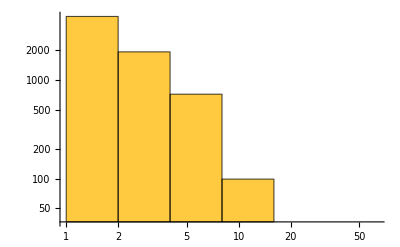

```mathematica
M = 100;
t = 50;
agentCount=300;
sampleCount = 1000;
agentPositions =  GenerateAgents[agentCount, M];
rateMatrix = SampleMarkovMatrix[M];
thresholds = SampleThresholds[M];

(* ;;, ;;, 2 Selects avalanche size, ;;, ;;, 1 selects start node*)
avalancheSizes = ParallelTable[Simulate[rateMatrix,thresholds,agentPositions, t], sampleCount][[;;, ;;, 2]] // Flatten ;
Histogram[avalancheSizes,{PowerRange[1, 100, 2]},  ScalingFunctions->{"Log", "Log"}, PlotRange->Full  ]
```

### Running the simulation for real Graph

```mathematica
wNaive = NaiveRateMatrix[170, g];
Export["wMatNaive.mx", wNaive];
```

```mathematica
wNaive = SparseArray[Import["wMatNaive.mx"]];
MatrixPlot[wNaive] // Rasterize
```

-Graphics-

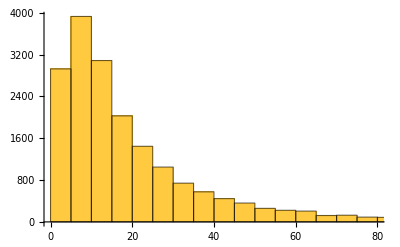

```mathematica
thresholds = GetRoadThresholds[g];
Histogram[thresholds]
```

```mathematica
$DefaultParallelKernels = {4};
CloseKernels[];
LaunchKernels[];
```

```mathematica
t = 20;
M = VertexCount@g;
agentCount=M/ 2; (*~10k*)
sampleCount = 500;
agentPositions =  GenerateAgents[agentCount, M];

simulationResults = ParallelTable[Simulate[wNaive,thresholds,agentPositions, t], sampleCount];
Export["resultsNaive.mx", simulationResults];
```

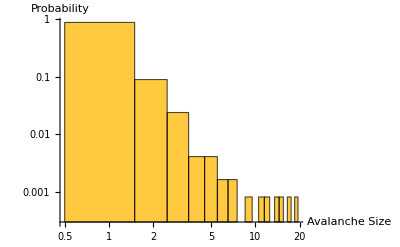

```mathematica
simulationResults = Import["resultsNaive.mx"];
avalancheSizes = simulationResults[[;;, ;;, 2]] // Flatten ;
Histogram[avalancheSizes,{1},  "Probability", ScalingFunctions->{"Log", "Log"}, PlotRange->Full, AxesLabel->{"Avalanche Size", "Probability"}  ]
```

```mathematica
coords = GetRoadCoordinates@g;
avalancheStartLocations = coords[[#]] &/@ Flatten@simulationResults[[;;, ;;, 1]] ;
```

```mathematica
avalancheGravity = {avalancheStartLocations, avalancheSizes};
GeoHistogram[WeightedData@@avalancheGravity, 50, PlotTheme->{"Scientific", "FrameGrid"}]
```

-Graphics-

```mathematica
GeoHistogram[avalancheStartLocations, 50, PlotTheme->"Classic"]
```

-Graphics-

## Fundamental Diagram

```mathematica
GetSpeedAndDensityOfSingleRoad = (edgeId) ↦ Module[{queryNodeCapacity, fluxValues, densityValues},
queryNodeCapacity = ExternalEvaluate[db, "
		SELECT
			t.hour_slot as time, AVG(t.count_mean / g.edge_length) AS density, AVG(t.speed_mean)*AVG(t.count_mean / g.edge_length) AS flux
		FROM traffic_data t
		INNER JOIN geo_edges g
		ON g.edge_id = t.edge_id AND ABS(t.edge_id) = "<>ToString[edgeId]<>"
		GROUP BY t.hour_slot
	;"];
fluxValues = Normal@Transpose[queryNodeCapacity]["flux"];
densityValues = Normal@Transpose[queryNodeCapacity]["density"];

{densityValues, fluxValues} // Transpose
];

PlotCongestionOfSingleRoad = (edgeId) ↦ Module[{},
ListPlot[GetSpeedAndDensityOfSingleRoad[edgeId], PlotRange->All]
];
```

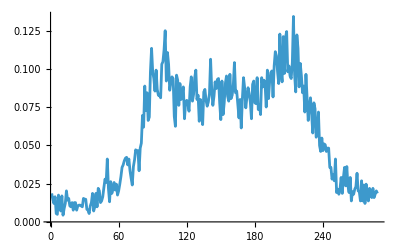

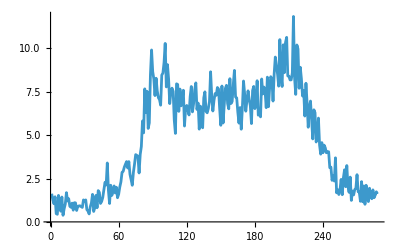

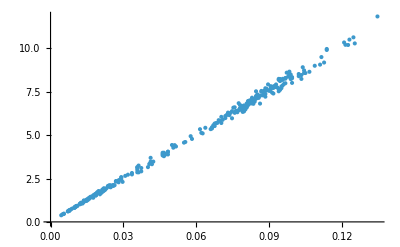

```mathematica
testRoad = GetSpeedAndDensityOfSingleRoad[55255453];
ListLinePlot[testRoad[[;;, 1]]]
ListLinePlot[testRoad[[;;, 2]]]
ListPlot[testRoad]
```

```mathematica
validNodes = VertexList[g];
$DefaultParallelKernels= {8};
CloseKernels[]
LaunchKernels[];
heatmapPoints = ParallelMap[GetSpeedAndDensityOfSingleRoad, validNodes, Method->"ItemsPerEvaluation" -> 10];
```

```mathematica
Export["heatmapPoints.mx", heatmapPoints];
```

```mathematica
heatmapPoints = Import["C:\\Users\\Matteo\\Documents\\heatmapPoints.mx"];
```

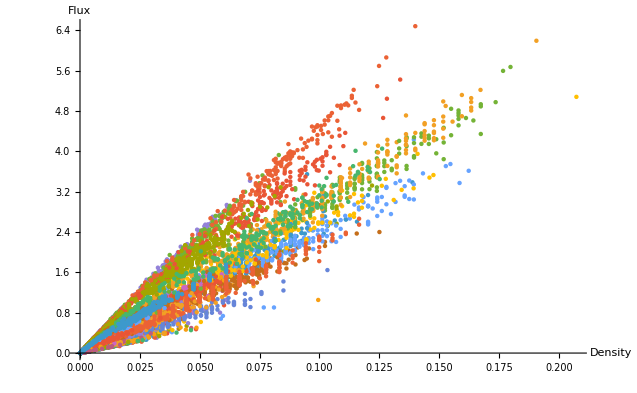

```mathematica
ListPlot[heatmapPoints[[200;;500]], AxesLabel->{"Density", "Flux"}, PlotStyle->PointSize[.005], PlotRange->Full]
```

### pocci

```mathematica
startTime = 80;
endTime = 83;
fractions = ParallelTable[Normal@GetTrafficAtHour[i][[;;100,2]], {i, startTime, endTime}];
```

```mathematica
M = VertexCount[g];
estimatedRates = EstimatedProcess[fractions,  DiscreteMarkovProcess[100]];
estimatedRates
```

```mathematica
EstimatedProcess[{{1, 1 ,1}, {2, 2, 2}, {3, 3, 3}, {1, 1, 1}}, DiscreteMarkovProcess[3]]
```

DiscreteMarkovProcess[{1/2,1/4,1/4},{{1,0,0},{0,1,0},{0,0,1}}]

```mathematica
𝒫=DiscreteMarkovProcess[3,{{1/2,1/2,0,0},{1/2,1/2,0,0},{1/4,1/4,1/4,1/4},{0,0,0,1}}];
p = StationaryDistribution[𝒫] // Normal
PDF[p, x]
```

ProbabilityDistribution[1/3 Boole[x==1]+1/3 Boole[x==2]+1/3 Boole[x==4],{x,1,4,1}]

Piecewise[{{1/3 Boole[x==1]+1/3 Boole[x==2]+1/3 Boole[x==4], 1≤x≤4}, {0, True}}]

```mathematica
{{1/2,1/2,0,0},{1/2,1/2,0,0},{1/4,1/4,1/4,1/4},{0,0,0,1}} // Eigenvectors
```

{{-1/2,-1/2,0,1},{3/2,3/2,1,0},{0,0,1,0},{-1,1,0,0}}

```mathematica
m = {{0, 1/3, 1/3},{1/2, 1/3, 1/3},{1/2, 1/3, 1/3}};
Eigenvalues[m]
Eigenvectors[m]
p = {0, -1, 1}
Norm[m.p] == 0
estim = {{a, b, c}, {d, e, f}, {g, h, i}};
eqns = {}
For[k=1, k<=3, k++, For[l = 1, l<=3, l++, AppendTo[eqns, estim[[k, l]]p[[k]] == estim[[l, k]]p[[l]]]]]
eqns
Solve[b==(2 d)/3&&c ==(2 g)/3 &&(2 d)/3==b && f==h &&(2 g)/3==c && a + d + g == 1 && b + e + h == 1 && c + f + i == 1] //N
```

```mathematica
$DefaultParallelKernels = {4}
CloseKernels[]
LaunchKernels[]
```

```mathematica
Mean[EstimatedProcess[data,Discere[n,n*n]][[2]]-markovMatrix//Flatten]
Variance[EstimatedProcess[data,HiddenMarkovProcess[n,n*n]][[2]]-markovMatrix//Flatten]
Mean[markovMatrix//Flatten]
Variance[markovMatrix//Flatten]
```

```mathematica
(*Pocci*)
proc = DiscreteMarkovProcess[statDist // Flatten, markovMatrix];
data = RandomFunction[proc, {0, 2}, agentCount];
Histogram[data]
```

```mathematica
GetTrafficAtHour[170]
```

Dataset[<>]